```mathematica
fermat=ReadList["/home/jirka/CPX/fermat2.txt"]//Sort;
ss=ReadList["/home/jirka/CPX/ss2.txt"]//Sort;
rm=ReadList["/home/jirka/CPX/rm2.txt"]//Sort;
```

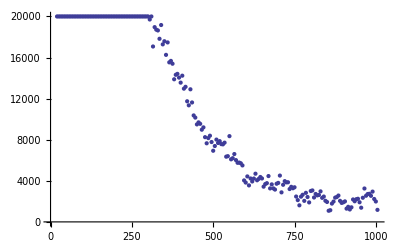

```mathematica
fermatLens={#[[1]],Length[#[[2]]]}&/@fermat;
ListPlot[fermatLens]
```

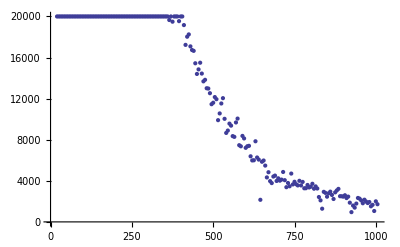

```mathematica
ssLens={#[[1]],Length[#[[2]]]}&/@ss;
ListPlot[ssLens]
```

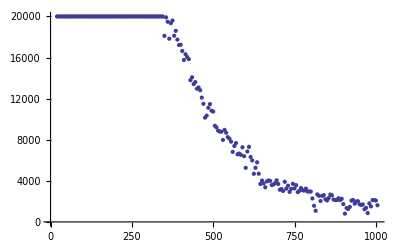

```mathematica
rmLens={#[[1]],Length[#[[2]]]}&/@rm;
ListPlot[rmLens]
```

```mathematica
Total[#[[2]]&/@fermatLens]
Total[#[[2]]&/@ssLens]
Total[#[[2]]&/@rmLens]
```

2034071

2311713

2176485

```mathematica
(Count[#[[2]],_?((#>0)&)]&/@fermat)//Total
(Cases[#[[2]],_?((#>0)&)])&/@fermat
```

8

{{},{1,1,1,1,11,1},{1,1},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
(Count[#[[2]],_?((#>0)&)]&/@ss)//Total
(Cases[#[[2]],_?((#>0)&)])&/@ss
```

3

{{},{1,1},{1},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
(Count[#[[2]],_?((#>0)&)]&/@rm)//Total
(Cases[#[[2]],_?((#>0)&)])&/@rm
```

3

{{},{1,1,1},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}